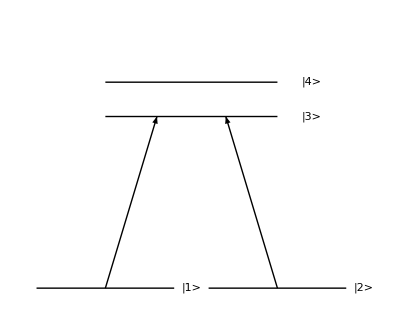

```mathematica
Graphics[{
Line[{{-4,0},{4,0}}],Text["|1>",{5,0}],
Line[{{6,0},{14,0}}],Text["|2>",{15,0}],
{AbsoluteThickness[1],Line[{{0,12},{10,12}}]},Text["|3>",{12,10}],
{AbsoluteThickness[1],Line[{{0,10},{10,10}}]},Text["|4>",{12,12}],
{Arrowheads[Large],Arrow[{{0,0},{3,10}}]},
{Arrowheads[Large],Arrow[{{10,0},{7,10}}]}}
,PlotRange->{-1,15},ImageSize->400]
```

# Calculating 4 Level

```mathematica
Clear[El,Elc,Ε,Γ,w,w1];
```

```mathematica
(*Same level transition is not allowed*)
Do[El[i,i]=0;Elc[i,i]=0;w[i,i]=0;Subscript[w, i,i]=0;w1[i,i]=0;,{i,1,4}];
(*Only allowing elctricfield on 1->3 1->4 2->3 2->4*)
Do[El[i,j]=0;Elc[i,j]=0,{i,1,2},{j,1,2}];Do[El[i,j]=0;Elc[i,j]=0,{i,3,4},{j,3,4}];
Ε [i_,j_]:=
If[i>j,El[i,j]Exp[-I w[i,j]t],Elc[j,i]Exp[I w[j,i]t]]/.Flatten[{w[#,1]-> wc,w[#,2]-> wp,El[#,1]->EC,El[#,2]->EP,Elc[#,1]->ECc,Elc[#,2]->EPc}&/@{3,4}]
(*Only allowing decay on 1->3 1->4 2->3 2->4*)
Do[If[!MemberQ[{{1,3},{1,4},{2,3},{2,4}},{i,j}],Γ[i,j]=0],{i,1,4},{j,1,4}];
(*1->3 and 1->4 are wc, and 2->3 and 2->4 are wp*)
w1[i_,j_]:=w[i,j]/.Flatten[{w[#,1]-> wc,w[#,2]-> wp,w[1,#]-> -wc,w[2,#]->-wp,w[2,1]->wc-wp,w[1,2]->-(wc-wp)}&/@{3,4}]
(*Rotating Frame except for the σ[3,4]*)
rot=DeleteCases[Flatten[Table[If[{i,j}≠ {3,4}&&{i,j}≠ {4,3},D[Subscript[ρ, i,j][t],t]-> D[Subscript[σ, i,j][t]Exp[-I (w1[i,j])t],t],D[Subscript[ρ, i,j][t],t]-> D[Subscript[σ, i,j][t],t]],{i,1,4},{j,1,4}]],Null];
rot1=DeleteCases[Flatten[Table[If[{i,j}≠ {3,4}&&{i,j}≠ {4,3},Subscript[ρ, i,j]->Subscript[σ, i,j][t]Exp[-I (w1[i,j])t],Subscript[ρ, i,j]->Subscript[σ, i,j][t]],{i,1,4},{j,1,4}]],Null];
```

```mathematica
(*Shrodinger equation for the density matrix equation*)
M=Table[D[Subscript[ρ, n,m][t],t]==-I (Subscript[w, n,m])Subscript[ρ, n,m]+I/ℏ Sum[Subscript[d, n,v] Ε[n,v] Subscript[ρ, v,m]-Subscript[ρ, n,v] Subscript[d, v,m] Ε[v,m],{v,1,4}]+If[n≠m,-Subscript[γ, n,m] Subscript[ρ, n,m],Sum[If[n≥ 3,-Γ[v,n] Subscript[ρ, n,n],Γ[n,v] Subscript[ρ, v,v]],{v,1,4}]],{n,1,4},{m,1,4}]//Expand;
(*Change the variable to the rabi frequency*)
M=M/.{Subscript[d, 3,1]->(ℏ ΩC)/(2 EC),Subscript[d, 1,3]->(ℏ ΩCc)/(2 ECc),Subscript[d, 4,1]->√(7/2)(ℏ ΩC)/(2 EC),Subscript[d, 1,4]->√(7/2)(ℏ ΩCc)/(2 ECc),Subscript[d, 3,2]->(ℏ ΩP)/(2 EP),Subscript[d, 2,3]->(ℏ ΩPc)/(2 EPc),Subscript[d, 4,2]->2/(√5)(ℏ ΩP)/(2 EP),Subscript[d, 2,4]->2/(√5)(ℏ ΩPc)/(2 EPc)};
M//TableForm
```

ρ_(1,1)'[t]==-1/2 ⅈ ⅇ^(-ⅈ t wc) ΩC ρ_(1,3)-1/2 ⅈ √(7/2) ⅇ^(-ⅈ t wc) ΩC ρ_(1,4)+1/2 ⅈ ⅇ^(ⅈ t wc) ΩCc ρ_(3,1)+1/2 ⅈ √(7/2) ⅇ^(ⅈ t wc) ΩCc ρ_(4,1)+ρ_(3,3) Γ[1,3]+ρ_(4,4) Γ[1,4] | ρ_(1,2)'[t]==-ⅈ w_(1,2) ρ_(1,2)-γ_(1,2) ρ_(1,2)-1/2 ⅈ ⅇ^(-ⅈ t wp) ΩP ρ_(1,3)-(ⅈ ⅇ^(-ⅈ t wp) ΩP ρ_(1,4))/(√5)+1/2 ⅈ ⅇ^(ⅈ t wc) ΩCc ρ_(3,2)+1/2 ⅈ √(7/2) ⅇ^(ⅈ t wc) ΩCc ρ_(4,2) | ρ_(1,3)'[t]==-1/2 ⅈ ⅇ^(ⅈ t wc) ΩCc ρ_(1,1)-1/2 ⅈ ⅇ^(ⅈ t wp) ΩPc ρ_(1,2)-ⅈ w_(1,3) ρ_(1,3)-γ_(1,3) ρ_(1,3)+1/2 ⅈ ⅇ^(ⅈ t wc) ΩCc ρ_(3,3)+1/2 ⅈ √(7/2) ⅇ^(ⅈ t wc) ΩCc ρ_(4,3) | ρ_(1,4)'[t]==-1/2 ⅈ √(7/2) ⅇ^(ⅈ t wc) ΩCc ρ_(1,1)-(ⅈ ⅇ^(ⅈ t wp) ΩPc ρ_(1,2))/(√5)-ⅈ w_(1,4) ρ_(1,4)-γ_(1,4) ρ_(1,4)+1/2 ⅈ ⅇ^(ⅈ t wc) ΩCc ρ_(3,4)+1/2 ⅈ √(7/2) ⅇ^(ⅈ t wc) ΩCc ρ_(4,4)
ρ_(2,1)'[t]==-ⅈ w_(2,1) ρ_(2,1)-γ_(2,1) ρ_(2,1)-1/2 ⅈ ⅇ^(-ⅈ t wc) ΩC ρ_(2,3)-1/2 ⅈ √(7/2) ⅇ^(-ⅈ t wc) ΩC ρ_(2,4)+1/2 ⅈ ⅇ^(ⅈ t wp) ΩPc ρ_(3,1)+(ⅈ ⅇ^(ⅈ t wp) ΩPc ρ_(4,1))/(√5) | ρ_(2,2)'[t]==-1/2 ⅈ ⅇ^(-ⅈ t wp) ΩP ρ_(2,3)-(ⅈ ⅇ^(-ⅈ t wp) ΩP ρ_(2,4))/(√5)+1/2 ⅈ ⅇ^(ⅈ t wp) ΩPc ρ_(3,2)+(ⅈ ⅇ^(ⅈ t wp) ΩPc ρ_(4,2))/(√5)+ρ_(3,3) Γ[2,3]+ρ_(4,4) Γ[2,4] | ρ_(2,3)'[t]==-1/2 ⅈ ⅇ^(ⅈ t wc) ΩCc ρ_(2,1)-1/2 ⅈ ⅇ^(ⅈ t wp) ΩPc ρ_(2,2)-ⅈ w_(2,3) ρ_(2,3)-γ_(2,3) ρ_(2,3)+1/2 ⅈ ⅇ^(ⅈ t wp) ΩPc ρ_(3,3)+(ⅈ ⅇ^(ⅈ t wp) ΩPc ρ_(4,3))/(√5) | ρ_(2,4)'[t]==-1/2 ⅈ √(7/2) ⅇ^(ⅈ t wc) ΩCc ρ_(2,1)-(ⅈ ⅇ^(ⅈ t wp) ΩPc ρ_(2,2))/(√5)-ⅈ w_(2,4) ρ_(2,4)-γ_(2,4) ρ_(2,4)+1/2 ⅈ ⅇ^(ⅈ t wp) ΩPc ρ_(3,4)+(ⅈ ⅇ^(ⅈ t wp) ΩPc ρ_(4,4))/(√5)
ρ_(3,1)'[t]==1/2 ⅈ ⅇ^(-ⅈ t wc) ΩC ρ_(1,1)+1/2 ⅈ ⅇ^(-ⅈ t wp) ΩP ρ_(2,1)-ⅈ w_(3,1) ρ_(3,1)-γ_(3,1) ρ_(3,1)-1/2 ⅈ ⅇ^(-ⅈ t wc) ΩC ρ_(3,3)-1/2 ⅈ √(7/2) ⅇ^(-ⅈ t wc) ΩC ρ_(3,4) | ρ_(3,2)'[t]==1/2 ⅈ ⅇ^(-ⅈ t wc) ΩC ρ_(1,2)+1/2 ⅈ ⅇ^(-ⅈ t wp) ΩP ρ_(2,2)-ⅈ w_(3,2) ρ_(3,2)-γ_(3,2) ρ_(3,2)-1/2 ⅈ ⅇ^(-ⅈ t wp) ΩP ρ_(3,3)-(ⅈ ⅇ^(-ⅈ t wp) ΩP ρ_(3,4))/(√5) | ρ_(3,3)'[t]==1/2 ⅈ ⅇ^(-ⅈ t wc) ΩC ρ_(1,3)+1/2 ⅈ ⅇ^(-ⅈ t wp) ΩP ρ_(2,3)-1/2 ⅈ ⅇ^(ⅈ t wc) ΩCc ρ_(3,1)-1/2 ⅈ ⅇ^(ⅈ t wp) ΩPc ρ_(3,2)-ρ_(3,3) Γ[1,3]-ρ_(3,3) Γ[2,3] | ρ_(3,4)'[t]==1/2 ⅈ ⅇ^(-ⅈ t wc) ΩC ρ_(1,4)+1/2 ⅈ ⅇ^(-ⅈ t wp) ΩP ρ_(2,4)-1/2 ⅈ √(7/2) ⅇ^(ⅈ t wc) ΩCc ρ_(3,1)-(ⅈ ⅇ^(ⅈ t wp) ΩPc ρ_(3,2))/(√5)-ⅈ w_(3,4) ρ_(3,4)-γ_(3,4) ρ_(3,4)
ρ_(4,1)'[t]==1/2 ⅈ √(7/2) ⅇ^(-ⅈ t wc) ΩC ρ_(1,1)+(ⅈ ⅇ^(-ⅈ t wp) ΩP ρ_(2,1))/(√5)-ⅈ w_(4,1) ρ_(4,1)-γ_(4,1) ρ_(4,1)-1/2 ⅈ ⅇ^(-ⅈ t wc) ΩC ρ_(4,3)-1/2 ⅈ √(7/2) ⅇ^(-ⅈ t wc) ΩC ρ_(4,4) | ρ_(4,2)'[t]==1/2 ⅈ √(7/2) ⅇ^(-ⅈ t wc) ΩC ρ_(1,2)+(ⅈ ⅇ^(-ⅈ t wp) ΩP ρ_(2,2))/(√5)-ⅈ w_(4,2) ρ_(4,2)-γ_(4,2) ρ_(4,2)-1/2 ⅈ ⅇ^(-ⅈ t wp) ΩP ρ_(4,3)-(ⅈ ⅇ^(-ⅈ t wp) ΩP ρ_(4,4))/(√5) | ρ_(4,3)'[t]==1/2 ⅈ √(7/2) ⅇ^(-ⅈ t wc) ΩC ρ_(1,3)+(ⅈ ⅇ^(-ⅈ t wp) ΩP ρ_(2,3))/(√5)-1/2 ⅈ ⅇ^(ⅈ t wc) ΩCc ρ_(4,1)-1/2 ⅈ ⅇ^(ⅈ t wp) ΩPc ρ_(4,2)-ⅈ w_(4,3) ρ_(4,3)-γ_(4,3) ρ_(4,3) | ρ_(4,4)'[t]==1/2 ⅈ √(7/2) ⅇ^(-ⅈ t wc) ΩC ρ_(1,4)+(ⅈ ⅇ^(-ⅈ t wp) ΩP ρ_(2,4))/(√5)-1/2 ⅈ √(7/2) ⅇ^(ⅈ t wc) ΩCc ρ_(4,1)-(ⅈ ⅇ^(ⅈ t wp) ΩPc ρ_(4,2))/(√5)-ρ_(4,4) Γ[1,4]-ρ_(4,4) Γ[2,4]

```mathematica
(*Change the density matrix to the rotating frame*)
M1=M/.rot/.rot1;
M2=Table[Solve[M1[[i,j]],Subscript[σ, i,j]'[t]],{i,1,4},{j,1,4}][[All,All,1,1,2]]//Simplify//Expand;
M2=M2/.DeleteCases[Flatten[Table[If[i<j,w[i,j]->-w[j,i]],{i,1,4},{j,1,4}]],Null]/.Flatten[Table[Subscript[σ, i,j][t]->Subscript[σ, i,j],{i,1,4},{j,1,4}]]/.DeleteCases[Flatten[Table[If[i<j,Subscript[w, i,j]->-Subscript[w, j,i]],{i,1,4},{j,1,4}]],Null];
M3=M2/.{ Subscript[w, 3,1]-> wc-Δ, Subscript[w, 4,1]->w43+wc-Δ, Subscript[w, 3,2]->(wp+δ-Δ), Subscript[w, 4,2]-> (wp+w43+δ-Δ), Subscript[w, 2,1]->(wc-wp-δ)}//ExpandAll;
%//TableForm
```

-1/2 ⅈ ΩC σ_(1,3)-1/2 ⅈ √(7/2) ΩC σ_(1,4)+1/2 ⅈ ΩCc σ_(3,1)+1/2 ⅈ √(7/2) ΩCc σ_(4,1)+σ_(3,3) Γ[1,3]+σ_(4,4) Γ[1,4] | -ⅈ δ σ_(1,2)-γ_(1,2) σ_(1,2)-1/2 ⅈ ΩP σ_(1,3)-(ⅈ ΩP σ_(1,4))/(√5)+1/2 ⅈ ΩCc σ_(3,2)+1/2 ⅈ √(7/2) ΩCc σ_(4,2) | -1/2 ⅈ ΩCc σ_(1,1)-1/2 ⅈ ΩPc σ_(1,2)-ⅈ Δ σ_(1,3)-γ_(1,3) σ_(1,3)+1/2 ⅈ ΩCc σ_(3,3)+1/2 ⅈ √(7/2) ΩCc σ_(4,3) | -1/2 ⅈ √(7/2) ΩCc σ_(1,1)-(ⅈ ΩPc σ_(1,2))/(√5)+ⅈ w43 σ_(1,4)-ⅈ Δ σ_(1,4)-γ_(1,4) σ_(1,4)+1/2 ⅈ ΩCc σ_(3,4)+1/2 ⅈ √(7/2) ΩCc σ_(4,4)
ⅈ δ σ_(2,1)-γ_(2,1) σ_(2,1)-1/2 ⅈ ΩC σ_(2,3)-1/2 ⅈ √(7/2) ΩC σ_(2,4)+1/2 ⅈ ΩPc σ_(3,1)+(ⅈ ΩPc σ_(4,1))/(√5) | -1/2 ⅈ ΩP σ_(2,3)-(ⅈ ΩP σ_(2,4))/(√5)+1/2 ⅈ ΩPc σ_(3,2)+(ⅈ ΩPc σ_(4,2))/(√5)+σ_(3,3) Γ[2,3]+σ_(4,4) Γ[2,4] | -1/2 ⅈ ΩCc σ_(2,1)-1/2 ⅈ ΩPc σ_(2,2)+ⅈ δ σ_(2,3)-ⅈ Δ σ_(2,3)-γ_(2,3) σ_(2,3)+1/2 ⅈ ΩPc σ_(3,3)+(ⅈ ΩPc σ_(4,3))/(√5) | -1/2 ⅈ √(7/2) ΩCc σ_(2,1)-(ⅈ ΩPc σ_(2,2))/(√5)+ⅈ w43 σ_(2,4)+ⅈ δ σ_(2,4)-ⅈ Δ σ_(2,4)-γ_(2,4) σ_(2,4)+1/2 ⅈ ΩPc σ_(3,4)+(ⅈ ΩPc σ_(4,4))/(√5)
1/2 ⅈ ΩC σ_(1,1)+1/2 ⅈ ΩP σ_(2,1)+ⅈ Δ σ_(3,1)-γ_(3,1) σ_(3,1)-1/2 ⅈ ΩC σ_(3,3)-1/2 ⅈ √(7/2) ΩC σ_(3,4) | 1/2 ⅈ ΩC σ_(1,2)+1/2 ⅈ ΩP σ_(2,2)-ⅈ δ σ_(3,2)+ⅈ Δ σ_(3,2)-γ_(3,2) σ_(3,2)-1/2 ⅈ ΩP σ_(3,3)-(ⅈ ΩP σ_(3,4))/(√5) | 1/2 ⅈ ΩC σ_(1,3)+1/2 ⅈ ΩP σ_(2,3)-1/2 ⅈ ΩCc σ_(3,1)-1/2 ⅈ ΩPc σ_(3,2)-σ_(3,3) Γ[1,3]-σ_(3,3) Γ[2,3] | 1/2 ⅈ ΩC σ_(1,4)+1/2 ⅈ ΩP σ_(2,4)-1/2 ⅈ √(7/2) ΩCc σ_(3,1)-(ⅈ ΩPc σ_(3,2))/(√5)+ⅈ w_(4,3) σ_(3,4)-γ_(3,4) σ_(3,4)
1/2 ⅈ √(7/2) ΩC σ_(1,1)+(ⅈ ΩP σ_(2,1))/(√5)-ⅈ w43 σ_(4,1)+ⅈ Δ σ_(4,1)-γ_(4,1) σ_(4,1)-1/2 ⅈ ΩC σ_(4,3)-1/2 ⅈ √(7/2) ΩC σ_(4,4) | 1/2 ⅈ √(7/2) ΩC σ_(1,2)+(ⅈ ΩP σ_(2,2))/(√5)-ⅈ w43 σ_(4,2)-ⅈ δ σ_(4,2)+ⅈ Δ σ_(4,2)-γ_(4,2) σ_(4,2)-1/2 ⅈ ΩP σ_(4,3)-(ⅈ ΩP σ_(4,4))/(√5) | 1/2 ⅈ √(7/2) ΩC σ_(1,3)+(ⅈ ΩP σ_(2,3))/(√5)-1/2 ⅈ ΩCc σ_(4,1)-1/2 ⅈ ΩPc σ_(4,2)-ⅈ w_(4,3) σ_(4,3)-γ_(4,3) σ_(4,3) | 1/2 ⅈ √(7/2) ΩC σ_(1,4)+(ⅈ ΩP σ_(2,4))/(√5)-1/2 ⅈ √(7/2) ΩCc σ_(4,1)-(ⅈ ΩPc σ_(4,2))/(√5)-σ_(4,4) Γ[1,4]-σ_(4,4) Γ[2,4]

```mathematica
(*Stable condition*)
M4=M3/.{Subscript[σ, 2,2]->1,Subscript[σ, 1,1]->0,Subscript[σ, 3,3]->0,Subscript[σ, 4,4]->0};
M4//TableForm
```

-1/2 ⅈ ΩC σ_(1,3)-1/2 ⅈ √(7/2) ΩC σ_(1,4)+1/2 ⅈ ΩCc σ_(3,1)+1/2 ⅈ √(7/2) ΩCc σ_(4,1) | -ⅈ δ σ_(1,2)-γ_(1,2) σ_(1,2)-1/2 ⅈ ΩP σ_(1,3)-(ⅈ ΩP σ_(1,4))/(√5)+1/2 ⅈ ΩCc σ_(3,2)+1/2 ⅈ √(7/2) ΩCc σ_(4,2) | -1/2 ⅈ ΩPc σ_(1,2)-ⅈ Δ σ_(1,3)-γ_(1,3) σ_(1,3)+1/2 ⅈ √(7/2) ΩCc σ_(4,3) | -(ⅈ ΩPc σ_(1,2))/(√5)+ⅈ w43 σ_(1,4)-ⅈ Δ σ_(1,4)-γ_(1,4) σ_(1,4)+1/2 ⅈ ΩCc σ_(3,4)
ⅈ δ σ_(2,1)-γ_(2,1) σ_(2,1)-1/2 ⅈ ΩC σ_(2,3)-1/2 ⅈ √(7/2) ΩC σ_(2,4)+1/2 ⅈ ΩPc σ_(3,1)+(ⅈ ΩPc σ_(4,1))/(√5) | -1/2 ⅈ ΩP σ_(2,3)-(ⅈ ΩP σ_(2,4))/(√5)+1/2 ⅈ ΩPc σ_(3,2)+(ⅈ ΩPc σ_(4,2))/(√5) | -(ⅈ ΩPc)/2-1/2 ⅈ ΩCc σ_(2,1)+ⅈ δ σ_(2,3)-ⅈ Δ σ_(2,3)-γ_(2,3) σ_(2,3)+(ⅈ ΩPc σ_(4,3))/(√5) | -(ⅈ ΩPc)/(√5)-1/2 ⅈ √(7/2) ΩCc σ_(2,1)+ⅈ w43 σ_(2,4)+ⅈ δ σ_(2,4)-ⅈ Δ σ_(2,4)-γ_(2,4) σ_(2,4)+1/2 ⅈ ΩPc σ_(3,4)
1/2 ⅈ ΩP σ_(2,1)+ⅈ Δ σ_(3,1)-γ_(3,1) σ_(3,1)-1/2 ⅈ √(7/2) ΩC σ_(3,4) | (ⅈ ΩP)/2+1/2 ⅈ ΩC σ_(1,2)-ⅈ δ σ_(3,2)+ⅈ Δ σ_(3,2)-γ_(3,2) σ_(3,2)-(ⅈ ΩP σ_(3,4))/(√5) | 1/2 ⅈ ΩC σ_(1,3)+1/2 ⅈ ΩP σ_(2,3)-1/2 ⅈ ΩCc σ_(3,1)-1/2 ⅈ ΩPc σ_(3,2) | 1/2 ⅈ ΩC σ_(1,4)+1/2 ⅈ ΩP σ_(2,4)-1/2 ⅈ √(7/2) ΩCc σ_(3,1)-(ⅈ ΩPc σ_(3,2))/(√5)+ⅈ w_(4,3) σ_(3,4)-γ_(3,4) σ_(3,4)
(ⅈ ΩP σ_(2,1))/(√5)-ⅈ w43 σ_(4,1)+ⅈ Δ σ_(4,1)-γ_(4,1) σ_(4,1)-1/2 ⅈ ΩC σ_(4,3) | (ⅈ ΩP)/(√5)+1/2 ⅈ √(7/2) ΩC σ_(1,2)-ⅈ w43 σ_(4,2)-ⅈ δ σ_(4,2)+ⅈ Δ σ_(4,2)-γ_(4,2) σ_(4,2)-1/2 ⅈ ΩP σ_(4,3) | 1/2 ⅈ √(7/2) ΩC σ_(1,3)+(ⅈ ΩP σ_(2,3))/(√5)-1/2 ⅈ ΩCc σ_(4,1)-1/2 ⅈ ΩPc σ_(4,2)-ⅈ w_(4,3) σ_(4,3)-γ_(4,3) σ_(4,3) | 1/2 ⅈ √(7/2) ΩC σ_(1,4)+(ⅈ ΩP σ_(2,4))/(√5)-1/2 ⅈ √(7/2) ΩCc σ_(4,1)-(ⅈ ΩPc σ_(4,2))/(√5)

```mathematica
(*Solve by the steady state approximation*)
M6=DeleteCases[Flatten[Table[If[i≠j,M4[[i,j]]]==0,{i,1,4},{j,1,4}]],Null==0];
list1=DeleteCases[Flatten[Table[If[i≠j,Subscript[σ, i,j]],{i,1,4},{j,1,4}]],Null];
f={};
(*Only for the first order of the prob*)
pat0=Times[_.,ΩPc|Power[ΩPc,_],ΩP|Power[ΩP,_]];
ser[expr_]:=DeleteCases[ExpandAll[expr],pat0,Infinity]
(*ser[expr_]:=PolynomialMod[expr,ΩP ΩPc]*)
Do[
Do[
list=list1;
ans=Solve[M6[[q]],list1[[k]]]//Simplify;
If[ans=={},list=Delete[list,k];,Break[];];
,{k,1,12}];
f=Append[f,ans[[1]]];
M6=ser[M6/.ans[[1]]]//Simplify;
Print[q];
,{q,1,12}]
```

1

2

3

4

5

6

7

$Aborted

```mathematica
F
```

F

```mathematica
f
```

{{σ_(1,2)→(-10 ΩP σ_(1,3)-4 √5 ΩP σ_(1,4)+5 ΩCc (2 σ_(3,2)+√14 σ_(4,2)))/(20 (δ-ⅈ γ_(1,2)))},{σ_(1,3)→-(ⅈ ΩCc (2 ΩPc σ_(3,2)+√14 (ΩPc σ_(4,2)-2 (δ-ⅈ γ_(1,2)) σ_(4,3))))/(8 (δ-ⅈ γ_(1,2)) γ_(1,3))},{σ_(1,4)→(ΩCc (2 ΩPc σ_(3,2)-2 √5 (δ-ⅈ γ_(1,2)) σ_(3,4)+√14 ΩPc σ_(4,2)))/(4 √5 (δ-ⅈ γ_(1,2)) (w43+ⅈ γ_(1,4)))},{σ_(2,1)→(10 ΩC σ_(2,3)+5 √14 ΩC σ_(2,4)-10 ΩPc σ_(3,1)-4 √5 ΩPc σ_(4,1))/(20 δ+20 ⅈ γ_(2,1))},{σ_(2,3)→(5 √14 ΩC ΩCc σ_(2,4)-4 ⅈ ΩPc γ_(2,1) (-5+2 √5 σ_(4,3))-2 ΩPc (-10 δ+5 ΩCc σ_(3,1)+2 √5 ΩCc σ_(4,1)+4 √5 δ σ_(4,3)))/(10 (4 δ^2-ΩC ΩCc+4 ⅈ γ_(2,1) (δ+ⅈ γ_(2,3))+4 ⅈ δ γ_(2,3)))},{σ_(2,4)→(ΩPc (16 √5 δ^2-4 √5 ΩC ΩCc+5 √14 ΩC ΩCc-10 √14 δ ΩCc σ_(3,1)+8 ⅈ γ_(2,1) (δ+ⅈ γ_(2,3)) (2 √5-5 σ_(3,4))-40 δ^2 σ_(3,4)+10 ΩC ΩCc σ_(3,4)-4 √70 δ ΩCc σ_(4,1)+2 ⅈ γ_(2,3) (8 √5 δ-5 √14 ΩCc σ_(3,1)-20 δ σ_(3,4)-2 √70 ΩCc σ_(4,1))-2 √70 ΩC ΩCc σ_(4,3)))/(10 (8 w43 δ^2+8 δ^3-2 w43 ΩC ΩCc-9 δ ΩC ΩCc+8 ⅈ γ_(2,1) (δ+ⅈ γ_(2,3)) (w43+δ+ⅈ γ_(2,4))+8 ⅈ δ^2 γ_(2,4)-2 ⅈ ΩC ΩCc γ_(2,4)+ⅈ γ_(2,3) (8 w43 δ+8 δ^2-7 ΩC ΩCc+8 ⅈ δ γ_(2,4))))},{σ_(3,1)→-(ⅈ √(7/2) ΩC σ_(3,4))/(2 γ_(3,1))},{σ_(3,2)→(-2 γ_(1,3) (-20 w43 δ ΩP+8 √5 w43 δ ΩP σ_(3,4)-2 √5 ΩC ΩCc ΩP σ_(3,4)+4 ΩP γ_(1,2) (-ⅈ w43+γ_(1,4)) (-5+2 √5 σ_(3,4))-5 √14 w43 ΩC ΩCc σ_(4,2)+ⅈ γ_(1,4) (-20 δ ΩP+8 √5 δ ΩP σ_(3,4)-5 √14 ΩC ΩCc σ_(4,2)))+5 √14 ΩC ΩCc ΩP (-ⅈ w43+γ_(1,4)) σ_(4,3))/(20 γ_(1,3) (w43+ⅈ γ_(1,4)) (4 δ^2-ΩC ΩCc+γ_(1,2) (-4 ⅈ δ-4 γ_(3,2))-4 ⅈ δ γ_(3,2)))},{σ_(3,4)→(4 √(14/5) ΩC ΩCc ΩPc γ_(3,1) (w43-δ+ⅈ γ_(1,4)+ⅈ γ_(3,2)) σ_(4,2))/((-4 δ^2+ΩC ΩCc+4 ⅈ δ γ_(3,2)+4 γ_(1,2) (ⅈ δ+γ_(3,2))) (-7 ⅈ w43 ΩC ΩCc+2 γ_(3,1) (ΩC ΩCc-4 w43 w_(4,3)-4 ⅈ w43 γ_(3,4))+γ_(1,4) (7 ΩC ΩCc-8 ⅈ w_(4,3) γ_(3,1)+8 γ_(3,1) γ_(3,4))))}}

```mathematica
Clear[ans]
(*Substitute the solutions, and find the coherent term of the density matrix*)
ans[1]=f[[12]];
Do[
ans[i]=ser[(f[[13-i]]/.Flatten[ans[#]&/@Table[j-1,{j,2,i}]])]//Simplify
,{i,2,12}]
sol=Table[ans[i],{i,1,12}][[All,1]];
sol//TableForm
```

σ_(4,3)→0
σ_(4,2)→(ΩP (8 √10 δ^2-8 √10 δ Δ+5 √7 ΩC ΩCc-2 √10 ΩC ΩCc-8 ⅈ √10 γ_(1,2) (δ-Δ-ⅈ γ_(3,2))-8 ⅈ √10 δ γ_(3,2)))/(5 √2 (8 w43 δ^2+8 δ^3-8 w43 δ Δ-16 δ^2 Δ+8 δ Δ^2-2 w43 ΩC ΩCc-9 δ ΩC ΩCc+9 Δ ΩC ΩCc-8 ⅈ γ_(1,2) (δ-Δ-ⅈ γ_(3,2)) (w43+δ-Δ-ⅈ γ_(4,2))-8 ⅈ δ^2 γ_(4,2)+8 ⅈ δ Δ γ_(4,2)+2 ⅈ ΩC ΩCc γ_(4,2)-ⅈ γ_(3,2) (8 w43 δ+8 δ^2-8 δ Δ-7 ΩC ΩCc-8 ⅈ δ γ_(4,2))))
σ_(4,1)→0
σ_(3,4)→0
σ_(3,2)→(ΩP (40 w43 δ+40 δ^2-40 δ Δ-35 ΩC ΩCc+2 √70 ΩC ΩCc-40 ⅈ γ_(1,2) (w43+δ-Δ-ⅈ γ_(4,2))-40 ⅈ δ γ_(4,2)))/(10 (8 w43 δ^2+8 δ^3-8 w43 δ Δ-16 δ^2 Δ+8 δ Δ^2-2 w43 ΩC ΩCc-9 δ ΩC ΩCc+9 Δ ΩC ΩCc-8 ⅈ γ_(1,2) (δ-Δ-ⅈ γ_(3,2)) (w43+δ-Δ-ⅈ γ_(4,2))-8 ⅈ δ^2 γ_(4,2)+8 ⅈ δ Δ γ_(4,2)+2 ⅈ ΩC ΩCc γ_(4,2)-ⅈ γ_(3,2) (8 w43 δ+8 δ^2-8 δ Δ-7 ΩC ΩCc-8 ⅈ δ γ_(4,2))))
σ_(3,1)→0
σ_(2,4)→(ΩPc (16 √5 δ^2-16 √5 δ Δ-4 √5 ΩC ΩCc+5 √14 ΩC ΩCc+16 ⅈ √5 γ_(2,1) (δ-Δ+ⅈ γ_(2,3))+16 ⅈ √5 δ γ_(2,3)))/(10 (8 w43 δ^2+8 δ^3-8 w43 δ Δ-16 δ^2 Δ+8 δ Δ^2-2 w43 ΩC ΩCc-9 δ ΩC ΩCc+9 Δ ΩC ΩCc+8 ⅈ γ_(2,1) (δ-Δ+ⅈ γ_(2,3)) (w43+δ-Δ+ⅈ γ_(2,4))+8 ⅈ δ^2 γ_(2,4)-8 ⅈ δ Δ γ_(2,4)-2 ⅈ ΩC ΩCc γ_(2,4)+ⅈ γ_(2,3) (8 w43 δ+8 δ^2-8 δ Δ-7 ΩC ΩCc+8 ⅈ δ γ_(2,4))))
σ_(2,3)→(ΩPc (40 √2 w43 δ+40 √2 δ^2-40 √2 δ Δ-35 √2 ΩC ΩCc+4 √35 ΩC ΩCc+40 ⅈ √2 γ_(2,1) (w43+δ-Δ+ⅈ γ_(2,4))+40 ⅈ √2 δ γ_(2,4)))/(10 √2 (8 w43 δ^2+8 δ^3-8 w43 δ Δ-16 δ^2 Δ+8 δ Δ^2-2 w43 ΩC ΩCc-9 δ ΩC ΩCc+9 Δ ΩC ΩCc+8 ⅈ γ_(2,1) (δ-Δ+ⅈ γ_(2,3)) (w43+δ-Δ+ⅈ γ_(2,4))+8 ⅈ δ^2 γ_(2,4)-8 ⅈ δ Δ γ_(2,4)-2 ⅈ ΩC ΩCc γ_(2,4)+ⅈ γ_(2,3) (8 w43 δ+8 δ^2-8 δ Δ-7 ΩC ΩCc+8 ⅈ δ γ_(2,4))))
σ_(2,1)→(2 ΩC ΩPc (5 w43+5 δ+√70 δ-5 Δ-√70 Δ+ⅈ √70 γ_(2,3)+5 ⅈ γ_(2,4)))/(5 (8 w43 δ^2+8 δ^3-8 w43 δ Δ-16 δ^2 Δ+8 δ Δ^2-2 w43 ΩC ΩCc-9 δ ΩC ΩCc+9 Δ ΩC ΩCc+8 ⅈ γ_(2,1) (δ-Δ+ⅈ γ_(2,3)) (w43+δ-Δ+ⅈ γ_(2,4))+8 ⅈ δ^2 γ_(2,4)-8 ⅈ δ Δ γ_(2,4)-2 ⅈ ΩC ΩCc γ_(2,4)+ⅈ γ_(2,3) (8 w43 δ+8 δ^2-8 δ Δ-7 ΩC ΩCc+8 ⅈ δ γ_(2,4))))
σ_(1,4)→0
σ_(1,3)→0
σ_(1,2)→(2 ΩCc ΩP (5 w43+5 δ+√70 δ-5 Δ-√70 Δ-ⅈ √70 γ_(3,2)-5 ⅈ γ_(4,2)))/(5 (8 w43 δ^2+8 δ^3-8 w43 δ Δ-16 δ^2 Δ+8 δ Δ^2-2 w43 ΩC ΩCc-9 δ ΩC ΩCc+9 Δ ΩC ΩCc-8 ⅈ γ_(1,2) (δ-Δ-ⅈ γ_(3,2)) (w43+δ-Δ-ⅈ γ_(4,2))-8 ⅈ δ^2 γ_(4,2)+8 ⅈ δ Δ γ_(4,2)+2 ⅈ ΩC ΩCc γ_(4,2)-ⅈ γ_(3,2) (8 w43 δ+8 δ^2-8 δ Δ-7 ΩC ΩCc-8 ⅈ δ γ_(4,2))))

```mathematica
d[i_,j_]:=If[i>j,ToExpression["d"<>ToString[i]<>ToString[j]],ToExpression["d"<>ToString[j]<>ToString[i]]]
χ[i_,j_]:=(2 Nat d[i,j]^2 Subscript[σ, i,j])/(e0 ℏ If[i>j,ΩP,ΩPc])/.sol
```

```mathematica
χ42=Evaluate[χ[4,2]/.{Subscript[γ, 1,2]->γ21,Subscript[γ, 3,2]->γ32,ΩC ΩCc->omegac1^2}/.Subscript[γ, 4,2]->γ42]//FullSimplify
χ32=Evaluate[χ[3,2]/.{Subscript[γ, 1,2]->γ21,Subscript[γ, 3,2]->γ32,ΩC ΩCc->omegac2^2}/.Subscript[γ, 4,2]->γ42]//FullSimplify
χ24=Evaluate[χ[2,4]/.{Subscript[γ, 2,1]->γ21,Subscript[γ, 2,3]->γ32,ΩC ΩCc->omegac1^2}/.Subscript[γ, 2,4]->γ42]//FullSimplify
χ23=Evaluate[χ[2,3]/.{Subscript[γ, 2,1]->γ21,Subscript[γ, 2,3]->γ32,ΩC ΩCc->omegac2^2}/.Subscript[γ, 2,4]->γ42]//FullSimplify
```

(√2 d42^2 Nat (-ⅈ (5 √7-2 √10) omegac1^2+8 √10 (γ21+ⅈ δ) (ⅈ γ32-δ+Δ)))/(5 e0 (omegac1^2 (2 ⅈ w43+7 γ32+2 γ42+9 ⅈ (δ-Δ))-8 (γ21+ⅈ δ) (-ⅈ γ32+δ-Δ) (w43-ⅈ γ42+δ-Δ)) ℏ)

-(d32^2 Nat ((-35+2 √70) omegac2^2+40 (-ⅈ γ21+δ) (w43-ⅈ γ42+δ-Δ)))/(5 e0 (omegac2^2 (2 w43-7 ⅈ γ32-2 ⅈ γ42+9 δ-9 Δ)+8 (γ21+ⅈ δ) (γ32+ⅈ (δ-Δ)) (w43-ⅈ γ42+δ-Δ)) ℏ)

(d42^2 Nat (-ⅈ (4 √5-5 √14) omegac1^2-16 √5 (γ21-ⅈ δ) (ⅈ γ32+δ-Δ)))/(5 e0 (-8 (γ21-ⅈ δ) (ⅈ γ32+δ-Δ) (w43+ⅈ γ42+δ-Δ)+omegac1^2 (-2 ⅈ w43+7 γ32+2 γ42-9 ⅈ δ+9 ⅈ Δ)) ℏ)

(d32^2 Nat ((35 √2-4 √35) omegac2^2-40 √2 (ⅈ γ21+δ) (w43+ⅈ γ42+δ-Δ)))/(5 √2 e0 (omegac2^2 (2 w43+7 ⅈ γ32+2 ⅈ γ42+9 δ-9 Δ)+8 (γ21-ⅈ δ) (γ32-ⅈ (δ-Δ)) (w43+ⅈ γ42+δ-Δ)) ℏ)

# Plot the Result

## Module

RBpress

```mathematica
Rbpress[T_]:=
(*
Calculates the vapor pressure of Na depending on the temprerature of the cell.;
Input variable: T:temperature[C];
Output variable: p=Na pressure[torr];
Formulas obtained from "Sodium D Line Data" by Daniel A.Steck;
http://steck.us/alkalidata
*)

Module[{T1,p,k,c,MRb,w0,Nat,dopp},
T1=T+273.15;
(*If[T1<39.31+273.15,p=10^(-94.04826-1961.258/T1-0.03771687*T1+42.57526*Log[10,T1])
,p=10^(15.88253-4529.635/T1+0.00058663*T1-2.99138*Log[10,T1])
];*)
p= If[T1<312.5,10^(9.863-4215/T1),10^(9.318-4040/T1)];(*Unit is in Pa*)
k=1.3806503 10^-23; (*Boltzman's contstant[J/K]*)
c=2.99792458 10^8;(*Speed of light[m/s]*)
MRb=1.409993119 10^-25;(*Rb 85 atomic mass[kg]*)
(*w0=2Pi 377.107385*10^12;(*Transition frequency for 85Rb D1 line*)
dopp=w0/c*Sqrt[2 k*T1/MRb];*)
w0=794.76728224*10^-9;(*Transition frequency for 85Rb D1 line*)
dopp=2Pi/w0*Sqrt[2k*T1/MRb];
Nat=p/(k*T1); (*units in m^-3*)

{Nat,dopp,p,Sqrt[3k*T1/MRb]}
]
```

Checking somthing

```mathematica
Eit[T_,P_,diam_,γ21_,δ_,d_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,w43,Δ,d32,d42,γ42,wp},

Δ=2Pi d*10^9;(*Raman detuning*)
Nat=Rbpress[T][[1]];
wp=(794.76728224*10^-9);
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
w43=2Pi(210.923*10^6) +2Pi(150.659*10^6) ;

omegac1=(1/ℏ Sqrt[1/(e0 c)]*d32*Sqrt[P/(Pi*(diam/2)^2)]); 
omegac2=(1/ℏ Sqrt[1/(e0 c)]*d42*Sqrt[P/(Pi*(diam/2)^2)]);
χ42=-(d42^2 Nat ΩPc ((4 √5-5 √14) omegac1^2+16 √5 (ⅈ γ21+δ) (wp-ⅈ γ32+Subscript[w, 2,3])))/(5 e0 ΩPC ℏ (omegac1^2 (9 wp-2 ⅈ γ42)+8 (wp-ⅈ γ32) (ⅈ wp+γ42) (γ21-ⅈ δ)+2 (omegac1^2+4 (ⅈ wp+γ32) (γ21-ⅈ δ)) Subscript[w, 2,4]+Subscript[w, 2,3] (7 omegac1^2+8 (ⅈ wp+γ42) (γ21-ⅈ δ)+8 (ⅈ γ21+δ) Subscript[w, 2,4])-7 ⅈ omegac1^2 Subscript[γ, 2,3]));
χ32=-(d32^2 Nat ΩPc ((35 √2-4 √35) omegac2^2+40 √2 (ⅈ γ21+δ) (wp-ⅈ γ42+Subscript[w, 2,4])))/(5 √2 e0 ΩPC ℏ (omegac2^2 (9 wp-2 ⅈ γ42)+8 (wp-ⅈ γ32) (ⅈ wp+γ42) (γ21-ⅈ δ)+2 (omegac2^2+4 (ⅈ wp+γ32) (γ21-ⅈ δ)) Subscript[w, 2,4]+Subscript[w, 2,3] (7 omegac2^2+8 (ⅈ wp+γ42) (γ21-ⅈ δ)+8 (ⅈ γ21+δ) Subscript[w, 2,4])-7 ⅈ omegac2^2 Subscript[γ, 2,3]));
χ42=(4 d42^2 Nat (γ21+ⅈ δ) (-ⅈ γ32+δ-Δ))/(e0 (-ⅈ omegac1^2 (w43-ⅈ (γ32+γ42+2 ⅈ (δ-Δ)))+4 (γ21+ⅈ δ) (-ⅈ γ32+δ-Δ) (w43-ⅈ γ42+δ-Δ)) ℏ);
χ32=(4 d32^2 Nat (γ21+ⅈ δ) (w43-ⅈ γ42+δ-Δ))/(e0 (-ⅈ omegac2^2 (w43-ⅈ (γ32+γ42+2 ⅈ (δ-Δ)))+4 (γ21+ⅈ δ) (-ⅈ γ32+δ-Δ) (w43-ⅈ γ42+δ-Δ)) ℏ);
f=(χ42+χ32);

Exp[-2Pi*0.0254/(2wp)Im[ f]]
]
```

Scanning by (Δ , δ)

```mathematica
Eit[T_,P_,diam_,γ21_,δ_,d_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,w43,Δ,d32,d42,γ42,wp},

Δ=2Pi d*10^9;(*Raman detuning*)
Nat=Rbpress[T][[1]];
wp=(794.76728224*10^-9);
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
w43=2Pi(210.923*10^6) +2Pi(150.659*10^6) ;

omegac1=(1/ℏ Sqrt[1/(e0 c)]*d32*Sqrt[P/(Pi*(diam/2)^2)]); 
omegac2=(1/ℏ Sqrt[1/(e0 c)]*d42*Sqrt[P/(Pi*(diam/2)^2)]);

χ42=(4 d42^2 Nat (γ21+ⅈ δ) (-ⅈ γ32+δ-Δ))/(e0 (-ⅈ omegac1^2 (w43-ⅈ (γ32+γ42+2 ⅈ (δ-Δ)))+4 (γ21+ⅈ δ) (-ⅈ γ32+δ-Δ) (w43-ⅈ γ42+δ-Δ)) ℏ);
χ32=(4 d32^2 Nat (γ21+ⅈ δ) (w43-ⅈ γ42+δ-Δ))/(e0 (-ⅈ omegac2^2 (w43-ⅈ (γ32+γ42+2 ⅈ (δ-Δ)))+4 (γ21+ⅈ δ) (-ⅈ γ32+δ-Δ) (w43-ⅈ γ42+δ-Δ)) ℏ);
f=(χ42+χ32);

Exp[-2Pi*0.0254/(2wp)Im[ f]]
]
```

```mathematica
EitL[T_,P_,diam_,γ21_,δ_,d_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,hbar,Δ,d32,d33,wp,χ1,pt,χ2,Δ1,Δ2,f},
Δ=2Pi d*10^9;(*Raman detuning*)
hbar=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
Δ1=2Pi(210.923*10^6)  +2Pi(150.659*10^6);
Δ2=0 ;
wp=(794.98*10^-9);

Nat=Rbpress[T][[1]];
γ32=2*Pi*5.75 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d33=Sqrt[4/27]*2.537717 10^-29;
omegac1= 1/hbar Sqrt[1/(e0 c)]*d32*Sqrt[P/(Pi*(diam/2)^2)];  (*Change Rabi frequency into angular frequency*)
omegac2= 1/hbar Sqrt[1/(e0 c)]*d33*Sqrt[P/(Pi*(diam/2)^2)];  (*Change Rabi frequency into angular frequency*)
χ1=I(Nat d32^2)/(e0 hbar) (γ21(omegac1^2/4+γ21 γ32)+δ^2 γ32)/((δ^2-(Δ+Δ2) δ-γ21 γ32-omegac1^2/4)^2+(δ γ32+(δ-(Δ+Δ2))γ21)^2);
χ2=I(Nat d33^2)/(e0 hbar) (γ21(omegac2^2/4+γ21 γ32)+δ^2 γ32)/((δ^2-(Δ-Δ1) δ-γ21 γ32-omegac2^2/4)^2+(δ γ32+(δ-(Δ-Δ1))γ21)^2);
f=χ1+χ2;
Exp[ - 2Pi*0.0254/(2wp)Im[ f]]
]
```

Scanning by (Δ1 Δ2)

```mathematica
Eit1[T_,P_,diam_,γ21_,delt_,d_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,w43,Δ,d32,d42,γ42,wp,δ},

Δ=2Pi d*10^9;(*Raman detuning*)
δ=2Pi delt-Δ;
Nat=Rbpress[T][[1]];
wp=(794.76728224*10^-9);
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
w43=2Pi(210.923*10^6) +2Pi(150.659*10^6) ;

omegac1=(1/ℏ Sqrt[1/(e0 c)]*d32*Sqrt[P/(Pi*(diam/2)^2)]); 
omegac2=(1/ℏ Sqrt[1/(e0 c)]*d42*Sqrt[P/(Pi*(diam/2)^2)]);

χ42=(4 d42^2 Nat (γ21+ⅈ δ) (-ⅈ γ32+δ-Δ))/(e0 (-ⅈ omegac1^2 (w43-ⅈ (γ32+γ42+2 ⅈ (δ-Δ)))+4 (γ21+ⅈ δ) (-ⅈ γ32+δ-Δ) (w43-ⅈ γ42+δ-Δ)) ℏ);
χ32=(4 d32^2 Nat (γ21+ⅈ δ) (w43-ⅈ γ42+δ-Δ))/(e0 (-ⅈ omegac2^2 (w43-ⅈ (γ32+γ42+2 ⅈ (δ-Δ)))+4 (γ21+ⅈ δ) (-ⅈ γ32+δ-Δ) (w43-ⅈ γ42+δ-Δ)) ℏ);
f=(χ42+χ32);

Exp[-2Pi*0.0254/(2wp)Im[ f]]
]
```

```mathematica
EitL1[T_,P_,diam_,γ21_,delt_,d_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,hbar,Δ,d32,d33,wp,χ1,pt,χ2,Δ1,Δ2,f,δ},

Δ=2Pi d*10^9;(*Raman detuning*)
δ=2Pi delt-Δ;
Nat=Rbpress[T][[1]];
hbar=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
Δ1=2Pi(210.923*10^6)  +2Pi(150.659*10^6);
Δ2=0 ;
wp=(794.98*10^-9);

Nat=Rbpress[T][[1]];
γ32=2*Pi*5.75 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d33=Sqrt[4/27]*2.537717 10^-29;
omegac1= 1/hbar Sqrt[1/(e0 c)]*d32*Sqrt[P/(Pi*(diam/2)^2)];  (*Change Rabi frequency into angular frequency*)
omegac2= 1/hbar Sqrt[1/(e0 c)]*d33*Sqrt[P/(Pi*(diam/2)^2)];  (*Change Rabi frequency into angular frequency*)
χ1=I(Nat d32^2)/(e0 hbar) (γ21(omegac1^2/4+γ21 γ32)+δ^2 γ32)/((δ^2-(Δ+Δ2) δ-γ21 γ32-omegac1^2/4)^2+(δ γ32+(δ-(Δ+Δ2))γ21)^2);
χ2=I(Nat d33^2)/(e0 hbar) (γ21(omegac2^2/4+γ21 γ32)+δ^2 γ32)/((δ^2-(Δ-Δ1) δ-γ21 γ32-omegac2^2/4)^2+(δ γ32+(δ-(Δ-Δ1))γ21)^2);
f=χ1+χ2;
Exp[ - 2Pi*0.0254/(2wp)Im[ f]]
]
```

## Scanning by (Δ , δ)

```mathematica
Manipulate[TimeConstrained[
Show[
Plot[{Eit[T,P/1000,1.4/1000,γ*10^6 ,δ*10^6,d+1.5],EitL[T,P/1000,1.4/1000,γ*10^6 ,δ*10^6,d+1.5]},{d,-3,0.5},PlotRange->{0,1.5},Frame->True,Axes->False,ImageSize->800,PlotLegends->{"4Level","2x3Level"},FrameLabel-> {"ν-ν_o (GHz) ","transmission"}],
ListPlot[If[plot=="On",{helo1[y,i],helo2[y,i],helo3[y,i]},{0,0,0,0,0}],Joined->True,PlotLegends->{"NC1","PR1","PR05"}]]
,5]
,Style["Thoery",12,Bold],{{T,30,"T (C)"},0,60},{{P,0,"P(mW)"},0,10},{{γ,1,"γ(MHz)"},0,1},{{δ,0,"δ(MHz)"},-5,5,0.001},{sep,-0.5,0.5},Delimiter,Style["Experiment",12,Bold],{{plot,"Off"},{"On","Off"}},{{i,1,"Detun"},1,26,1},{{y,1,"Power"},{1->"6mV",2->"3mW",3->"No Pump"}}
]
```

```mathematica
812
```

```mathematica
162
```

## Scanning by (Δ1 Δ2)

```mathematica
Manipulate[TimeConstrained[
Plot[{Eit1[T,P/1000,1.4/1000,γ*10^6 ,δ*10^6,d],EitL1[T,P/1000,1.4/1000,γ*10^6 ,δ*10^6,d]},{d,-(x-y),-(x+y)},PlotRange->{0,1.5},Frame->True,Axes->False,PlotPoints->200,ImageSize->1020,PlotLegends->{"4Level","2x3Level"},FrameLabel-> {"ν-ν_o (GHz) ","transmission"}]
,5]
,{{T,30,"T (C)"},0,60},{{P,0,"P(mW)"},0,10},{{γ,1,"γ(MHz)"},0,1},{{δ,0,"δ(MHz)"},-100,400,0.001},{{x,0,"Plot Center"},-0.3,0.3,0.01},{{y,0.05,"Plot Width"},0.01,0.5}]
```

# Testing Doppler

```mathematica
Eit[T_,P_,diam_,γ21_,δ_,d_] :=
Module[{dopp,u,Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,w43,Δ,d32,d42,γ42,wp,t1,t2},

Δ=2Pi d*10^9;(*Raman detuning*)
Nat=Rbpress[T][[1]];
dopp=Rbpress[T][[1]];

wp=(794.76728224*10^-9);
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
w43=2Pi(210.923*10^6) +2Pi(150.659*10^6) ;
u=(c dopp)/(2 wp Sqrt[Log[2]]); 
omegac1=(1/ℏ Sqrt[1/(e0 c)]*d32*Sqrt[P/(Pi*(diam/2)^2)]); 
omegac2=(1/ℏ Sqrt[1/(e0 c)]*d42*Sqrt[P/(Pi*(diam/2)^2)]);

t1=-((4 ⅈ c d42^2 ⅇ^(-v^2/u^2) Nat (γ21+ⅈ δ) (v wp+c (ⅈ γ32-δ+Δ)))/(e0 √π u (4 ⅈ v^2 wp^2 (γ21+ⅈ δ)-2 c v wp (omegac1^2+2 (γ21+ⅈ δ) (ⅈ w43+γ32+γ42+2 ⅈ (δ-Δ)))+c^2 (omegac1^2 (w43-ⅈ (γ32+γ42+2 ⅈ (δ-Δ)))+4 (γ21+ⅈ δ) (γ32+ⅈ (δ-Δ)) (w43-ⅈ γ42+δ-Δ))) ℏ));
t2=(4 c d32^2 ⅇ^(-v^2/u^2) Nat (γ21+ⅈ δ) (-v wp+c (w43-ⅈ γ42+δ-Δ)))/(e0 √π u (4 v^2 wp^2 (γ21+ⅈ δ)+2 ⅈ c v wp (omegac2^2+2 (γ21+ⅈ δ) (ⅈ w43+γ32+γ42+2 ⅈ (δ-Δ)))+c^2 (-ⅈ omegac2^2 (w43-ⅈ (γ32+γ42+2 ⅈ (δ-Δ)))+4 (γ21+ⅈ δ) (-ⅈ γ32+δ-Δ) (w43-ⅈ γ42+δ-Δ))) ℏ);

f=NIntegrate[t1,{v,-10000,10000}]+NIntegrate[t2,{v,-10000,10000}];

Exp[-2Pi*0.0254/(2wp)Im[ f]]
]
```